#### Needs

```mathematica
Needs["PlotLegends`"];
Needs["Integration`NIntegrateUtilities`"];
```

#### Variables

```mathematica
F = 0.1;
Sw [ω_,r_,fi_,t_]:=(r^2 ω)/(2 t)+(F r)/ω(Sin[fi]+1/t(Cos[fi+t]-Cos[fi]))-F^2/(2 ω^3)(t - 2/t(1-Cos[t]))-t/(2ω);
Sdw[ω_,r_,fi_,t_]:=-(r^2 ω)/(2 t^2) -(F r)/(ω t)(Sin[fi+t]+1/t(Cos[fi+t]-Cos[fi]))-F^2/(2 ω^3)(1- 1/t 2Sin[t]+ 2/t^2(1-Cos[t]))-1/(2ω);
Sddw[ω_,r_,fi_,t_]:=F^2/(t ω^3)(Cos[t]- 1/t 2Sin[t]+ 2/t^2(1-Cos[t]))-(F r)/(ω t)(Cos[fi+t]-1/t 2Sin[fi+t]-2/t^2(Cos[fi+t]-Cos[fi]));
Sddmain[ω_,t_]:=F^2/(t ω^3)(Cos[t]- 1/t 2Sin[t]+ 2/t^2(1-Cos[t]));
Sdmain[t_]:=1- 1/t 2Sin[t]+ 2/t^2(1-Cos[t]);
grw[ω_,r_,fi_,t_]:=Exp[I Sw[ω,r,fi,t]]/(t ^(3/2));
```

#### Analytical SP

```mathematica
SPxyfixed[w_,x_,y_,n_]:=
If[x==0,
If[y==0,
N[I + I ProductLog[n,-1/E]],N[I + I ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[I ArcTan[x,y]])/(E F)]]],N[I + I ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[I ArcTan[x,y]])/(E F)]]];
SPxyfixedSECOND[w_,x_,y_,n_]:=
If[x==0,
If[y==0,
I + I ProductLog[n,-1/E],
-I - I ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[-I ArcTan[x,y]])/(E F)]],
-I - I ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[-I ArcTan[x,y]])/(E F)]];
```

```mathematica
SPfixed[n_]:=I+I ProductLog[n,-1/E];
SPfixedSecond[n_]:=-I- I ProductLog[n,-1/E];
```

#### Exact Solution

```mathematica
SPmovingXY[w_,x_,y_, n_]:=Module[{aa,bb},
If[x==0,
If[y==0,
aa=N[Re[I + I( ProductLog[n,-1/E])]];
bb=N[Im[I + I( ProductLog[n,-1/E])]];,
aa=N[Re[I + I( ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[I ArcTan[x,y]])/(E F)])]];
bb=N[Im[I + I (ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[I ArcTan[x,y]])/(E F)])]];],
aa=N[Re[I + I( ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[I ArcTan[x,y]])/(E F)])]];
bb=N[Im[I + I (ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[I ArcTan[x,y]])/(E F)])]]];
(a/.FindRoot[{ComplexExpand[Re[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0,
ComplexExpand[Im[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0},
{{a,aa},{b,bb}}])+I(b/.FindRoot[{ComplexExpand[Re[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0,
ComplexExpand[Im[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0},
{{a,aa},{b,bb}}])
];
SPmovingXYsecond[w_,x_,y_, n_]:=Module[{aa,bb},
If[x==0,
If[y==0,
aa=N[Re[-I - I( ProductLog[n,-1/E])]];
bb=N[Im[-I - I( ProductLog[n,-1/E])]];,
aa=N[Re[-I - I( ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[-I ArcTan[x,y]])/(E F)])]];
bb=N[Im[-I - I (ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[-I ArcTan[x,y]])/(E F)])]];],
aa=N[Re[-I - I( ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[-I ArcTan[x,y]])/(E F)])]];
bb=N[Im[-I - I (ProductLog[n,-1/E+(w^2 √(x^2+y^2) Exp[-I ArcTan[x,y]])/(E F)])]]];
(a/.FindRoot[{ComplexExpand[Re[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0,
ComplexExpand[Im[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0},
{{a,aa},{b,bb}}])+I(b/.FindRoot[{ComplexExpand[Re[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0,
ComplexExpand[Im[Sdw[w,√(x^2+y^2),ArcTan[x,y],a+I b]]]==0},
{{a,aa},{b,bb}}])
];
```

#### SaddlePoint Integral

```mathematica
SaddlePoint[w_,r_,fi_,sp_]:=Sqrt[(2 Pi)/(-Sddw[w,r,fi,sp]I)]grw[w,r,fi,sp];
SaddlePointmain[w_,r_,fi_,sp_]:=Sqrt[(2 Pi)/(-Sddmain[w,sp]I)]grw[w,r,fi,sp];
```

#### Contour Integration

```mathematica
Subscript[γ, 1][t_]:=4.105-I t;(* t from 5.401 to  2.870451357341934 *)
Subscript[γ, 2][t_]:=-2.870451357341934I+t ;(* t from 4.105 to  *)
Subscript[γ, 3][t_]:=10.29-I t;(* t from 2 to Infinity *)
```

```mathematica
(NIntegrate[grw[w, 1,1,Subscript[γ, 1][t]] Subscript[γ, 1]'[t],{t,5.401,2.870451357341934},
Method->{"GaussKronrod", "Points"->50},MaxRecursion->20, WorkingPrecision->50,
IntegrationMonitor:>((errors1=Through[#1@"Error"])&)]+
NIntegrate[grw[w,1,1,Subscript[γ, 2][t]] Subscript[γ, 2]'[t],{t,4,11},
Method->{"GaussKronrod", "Points"->50},MaxRecursion->20, WorkingPrecision->50,
IntegrationMonitor:>((errors2=Through[#1@"Error"])&)]
+NIntegrate[grw[w,1,1,Subscript[γ, 3][t]] Subscript[γ, 3]'[t],{t,2.870451357341934,5.411},
Method->{"GaussKronrod", "Points"->50},MaxRecursion->20, WorkingPrecision->50,
IntegrationMonitor:>((errors3=Through[#1@"Error"])&)])
```

#### Integration

```mathematica
TableForm[Table[Block[{e=0},{method,NIntegrate[g[1,1,t],{t,10^-3,1}, Method-> method,EvaluationMonitor:>e++,IntegrationMonitor:>((errors=Through[#1@"Error"])&)],Total@errors,Length@errors,e,
"Timing"/.NIntegrateProfile[NIntegrate[g[1,1,t],{t,1,Infinity}, Method-> method]]}],{method,methods}],TableHeadings->{{},{"Method","Value","Error", "Subintervals","Evaluations","Timing"}}]
```

#### Display

```mathematica
GraphicsRow[{p1,p2}]
```

```mathematica
Plot[{f[w]},{w,0.05,0.1},
PlotPoints->40,PlotRange->All,
AxesLabel->(Text[Style[#,Italic,13]]&/@{"ω","Im[I]"})]
```

```mathematica
TableForm[Table[{f1, f2},{w,0.01,0.1,0.01}],
TableHeadings->{Range[0.01,0.1,0.01],{"h1","h2"}}]
```

#### ContourPlot

```mathematica
plt111=StreamPlot[
Evaluate@{ReX,ReY},
{u,-15,15},{v,-15,15},
Epilog->{PointSize[0.01],Blue,Point[#]&/@pts111,Black},
StreamStyle->LightGray,
StreamPoints->200,
StreamScale->0.07];
cont111 =ContourPlot[
ComplexExpand[Im[Sn[x,y,a,b]]]==Im[Sn[x,y,pts1x,pts1y]],
{a,-15,15},{b,-15,15},
PlotLegends->Automatic,
FrameLabel->(Text[Style[#,Italic,16]]&/@{"Re z","Im z"}),
Epilog->{PointSize[0.01],Black,Point[#]&/@pts111,Black},
ContourStyle->Blue,
WorkingPrecision->100];
```

```mathematica
Show[plt111,cont111]
```

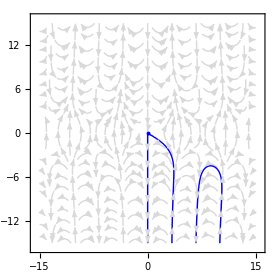

```mathematica
FOR
```

```mathematica
For[n=1,n≤10,n++,
w=n/100;r=10;fi=1;
z=SPmoving[w,r,fi];

bleft=blefts[[n]];
bright=brights[[n]];
rel=relefts[[n]];
rer=rerights[[n]];

Subscript[γ, 1][t_]:=rel+I t;(* t from bleft to Im[z] *)
Subscript[γ, 2][t_]:=Im[z] I+t ;(* t from rel to rer*)
Subscript[γ, 3][t_]:=rer+I t;(* t from Im[z] to bright *)

tbl={Round[w,0.001],
ScientificForm[ii=SaddlePoint[w,r,fi,SPmoving[w,r,fi]],2],
ScientificForm[jj=SaddlePointmain[w,r,fi,SPfixed],2],
ScientificForm[qq=(NIntegrate[grw[w, r,fi,Subscript[γ, 1][t]] Subscript[γ, 1]'[t],{t,bleft, Im[z]},
Method->{"GaussKronrod", "Points"->50},MaxRecursion->20, WorkingPrecision->50,
IntegrationMonitor:>((errors1=Through[#1@"Error"])&)]+
NIntegrate[grw[w,r,fi,Subscript[γ, 2][t]] Subscript[γ, 2]'[t],{t,rel,rer},
Method->{"GaussKronrod", "Points"->50},MaxRecursion->20, WorkingPrecision->50,
IntegrationMonitor:>((errors2=Through[#1@"Error"])&)]
+NIntegrate[grw[w,r,fi,Subscript[γ, 3][t]] Subscript[γ, 3]'[t],{t,Im[z],bright},
Method->{"GaussKronrod", "Points"->50},MaxRecursion->20, WorkingPrecision->50,
IntegrationMonitor:>((errors3=Through[#1@"Error"])&)]),4],
ScientificForm[Total@errors1+Total@errors2+Total@errors3,2],
Round[ N[ii/qq],0.0001],
Round[ N[jj/qq],0.0001]};
AppendTo[TheTable,tbl]];
```